```mathematica
d=2;r=1/4 π+50*2π;r/(2π)//N
```

50.125

```mathematica
f[x_]:=NIntegrate[BesselJ[d/2-1,r*z]/z^(d/2-1)*((d-1)π^((d-1)/2))/Gamma[(d+1)/2]*(√(z^2-x^2))^(d-3)*z,{z,x,1}]
g[x_]:=(2Cos[r*x])/(r)^(d/2)(2π)^(d/2-1)
```

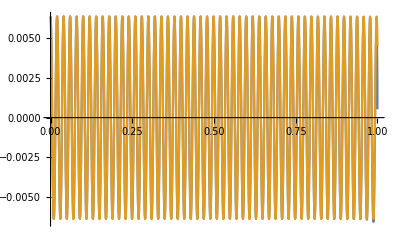

```mathematica
Plot[{f[x],g[x]},{x,0,1}]
```

```mathematica
Integrate[BesselJ[d/2-1,r*z]/z^(d/2-1)*((d-1)π^((d-1)/2))/Gamma[(d+1)/2]*(√(z^2-0^2))^(d-3)*z,{z,1,∞},PrincipalValue->True]
```

ConditionalExpression[(2^(-1-d/2) (-1+d) π^(-1/2+1/2 (-1+d)) r^(-1-d/2) Gamma[1/2 (-1+d)] (2^d r-2 √π r^d HypergeometricPFQRegularized[{1/2 (-1+d)},{(1+d)/2,d/2},-r^2/4]))/Gamma[(1+d)/2], Re[r]≥0&&(Im[r]>0||Re[r]>0)]

```mathematica
h[x_,r_]:=Sin[r*x]/x
```

```mathematica
J[r_]:=NIntegrate[x^2(h'[x,r])^2,{x,0,1}]
```

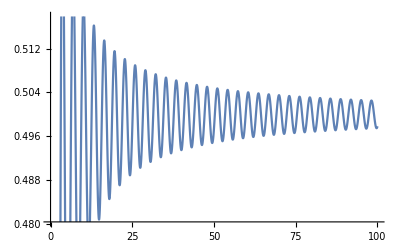

```mathematica
Plot[J[r]/r^2,{r,0,100}]
```